```mathematica
ClearAll["Global`*"]
```

## Q.Find the two largest maximums of an interpolating function of a specific shape (fast)

I have an oscillating interpolating function f[x] and I would like to find the x values of the two largest maximums (or even better: their distance).
One example of such an interpolating function is generated by this code:
v0 = 2 10^-5;
h = 1/50; 
a = -10; 
b = 10; 
plist = Range[N@a, b, h]; 
ψpi = E^(-(p^2/4)) (2/π)^(1/4) /. p -> plist;
ham = With[{c = N[I v0/(8 h^3)]}, 
   SparseArray[{Band[{1, 1}] -> 1./4 plist^2 + 0. I, 
     Band[{1, 4}] -> c, Band[{1, 3}] -> -8 c, Band[{1, 2}] -> +13 c, 
     Band[{2, 1}] -> -13 c, Band[{3, 1}] -> +8 c, 
     Band[{4, 1}] -> -c}, {1, 1} Length[plist], 0. + 0. I]];
ψp[t_, ψp0_] := ψp[t, ψp0] = 
   MatrixExp[ham/I (2. Pi t), ψp0]; 
f[t_] := f[t] = 
  Interpolation[Transpose[{plist, Abs[ψp[t, ψpi]]^2}]]
Plot[f[10][x], {x, -5, 5}, PlotRange -> All, PlotStyle -> Blue]

## Answer :

### As far as I understand you want to find x - coordinates of the two maximum peak values.I guess using FindPeaks can be useful in this case :

```mathematica
v0=2 10^-5;
h=1/50;
a=-10;
b=10;
plist=Range[N@a,b,h];
ψpi=E^(-(p^2/4)) (2/π)^(1/4)/.p->plist;
ham=With[{c=N[I v0/(8 h^3)]},SparseArray[{Band[{1,1}]->1./4 plist^2+0. I,Band[{1,4}]->c,Band[{1,3}]->-8 c,Band[{1,2}]->+13 c,Band[{2,1}]->-13 c,Band[{3,1}]->+8 c,Band[{4,1}]->-c},{1,1} Length[plist],0.+0. I]];
ψp[t_,ψp0_]:=ψp[t,ψp0]=MatrixExp[ham/I (2. Pi t),ψp0];
f[t_]:=f[t]=Interpolation[Transpose[{plist,Abs[ψp[t,ψpi]]^2}]]
```

```mathematica
d=Table[{x,f[10][x]},{x,-5,5,.01}];
Fp=FindPeaks[d[[All,2]]];
data1=Map[{d[[All,1]][[#[[1]]]],#[[2]]}&,Fp];
```

### Now, just sort it

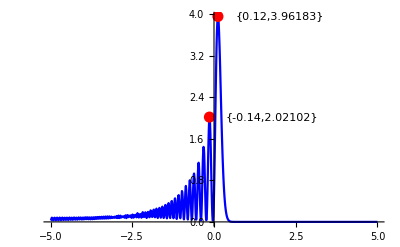

```mathematica
sorted=Sort[data1,Last[#2]<Last[#1]&];

cords=sorted[[1;;2]];
tex=cords;
offset=Map[#+{1.9,0}&,cords];
ListLinePlot[d,Joined->{True,False},PlotStyle->{Blue},PlotRange->All,Epilog->{Thread[Text[tex,offset]],Red,PointSize[0.02],Point[cords]},BaseStyle->{FontSize->14}]
```